## Single Pendulum

```mathematica
SinglePendulum[w_, v0_, tmax_] := Module[{s, t, y},
 s =  NDSolve[{Sin[y[t]]+ w y''[t]==0, y[0]==0, y'[0]== v0}, y, {t, 0, tmax}];
y[t] /. s]
```

```mathematica
s = SinglePendulum[1.0, 1.9999999, 200][t]
```

{InterpolatingFunction[{{0., 200.}}, <>][t$125127]}[t]

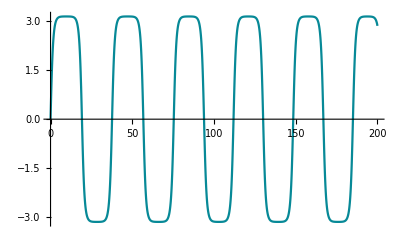

```mathematica
Plot[s, {t$121318, 0,200}, PlotRange -> All]
```